```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY207/sec_int_data/610nm.dat"]
```

{{1.65577,0.144966},{1.59352,0.155464},{1.51672,0.171934},{1.46373,0.210909},{1.42047,0.209531},{1.37769,0.231191},{1.34607,0.24467},{1.31418,0.244748},{1.27734,0.243181},{1.24989,0.232935},{1.21939,0.267658},{1.20221,0.257661},{1.18519,0.242632},{1.17023,0.239174},{1.1572,0.216481},{1.14604,0.205224},{1.13497,0.192932},{1.12762,0.134269},{1.12192,0.189545},{1.11852,0.17286},{1.11638,0.178397},{1.11532,0.180069},{1.11466,0.276571},{1.11691,0.271705},{1.12052,0.310935},{1.12514,0.311887},{1.15252,0.270638},{1.18204,0.238859},{1.20774,0.320851},{1.24068,0.315322},{1.28541,0.304244},{1.36328,0.282242},{1.4246,0.286156}}

0.343478-0.0865234 x

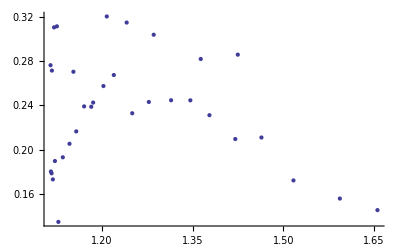

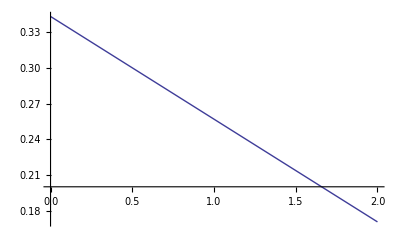

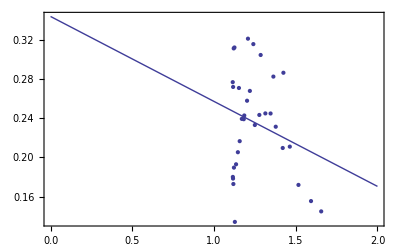

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```